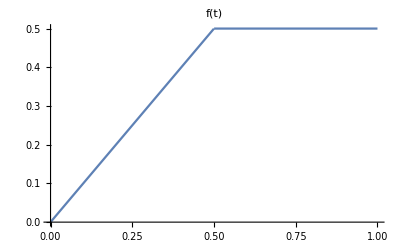

```mathematica
ClearAll[t,n,f,fSeries,an,bn];
T0=1;(*period*)f[t_]:=Piecewise[{{t,0<t<1/2},{1/2,1/2<t<T0},{0,True}}];
Plot[f[t],{t,0,T0},PlotLabel->"f(t)"]
```

```mathematica
D[f[t],t]
```

Piecewise[{{0, t<0}, {1, 0<t<1/2}, {0, 1/2<t<1||t>1}, {Indeterminate, True}}]

```mathematica
an[n_]=If[n==0,1/(T0) Integrate[f[t],{t,0,T0}],2/T0 Integrate[f[t] Cos[n 2 Pi/T0 t],{t,0,T0}]];
bn[n_]=2/T0 Integrate[f[t] Sin[n 2 Pi/T0 t],{t,0,T0}];
fSeries[t_,max_]:=an[0]+Sum[an[n] Cos[n 2 Pi/T0 t]+bn[n] Sin[n 2 Pi/T0 t],{n,1,max}];
```

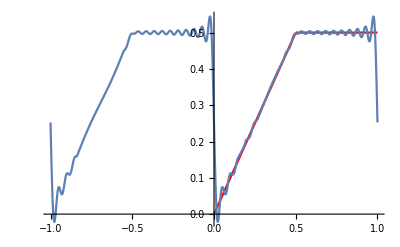

```mathematica
nTerms=20;
Show[Plot[f[t],{t,0,T0},PlotStyle->{Red}],Plot[Evaluate@fSeries[t,nTerms],{t,-T0,T0}],PlotRange->All]
```